#### Some useful constants

```mathematica
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
m={12.0107,91.224,1};ang2bohr=1/0.529177208;ev2har=1/27.211396;eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
```

#### DFT data: energy-volume and energy-displacement numbers

```mathematica
(*Volumes and energies*)
volperf={766.060875,778.68799,791.45312,808.7083508,822.6569529,846.5905360,862.257739832,885.289075,912.67299};e0perf={-.67382051*10^3,-.67479111*10^3,-.67540188*10^3,-.67568572*10^3,-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};e0cvac={-.66257856,-.66353617,-.66414458,-.66444074,-.66427725,-.66324766,-.66211597,-.65987660,-.65643966}*10^3;

(*Import V-nn (Zr) and V-nnn (C) data *)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS"]
filesC={"4.575.C.out","4.600.C.out","4.625.C.out","4.65837.C.out","4.685.C.out","4.730.C.out","4.759.C.out","4.801.C.out","4.850.C.out"};filesZr={"4.575.Zr.out","4.600.Zr.out","4.625.Zr.out","4.65837.Zr.out","4.685.Zr.out","4.730.Zr.out","4.759.Zr.out","4.801.Zr.out","4.850.Zr.out"};
CdataFull=Table[ReadList[filesC[[i]],{Number,Number,Word,Word,Number,Number,Number,Number}],{i,1,Length@filesC}];ZrdataFull=Table[ReadList[filesZr[[i]],{Number,Number,Word,Word,Number,Number,Number,Number}],{i,1,Length@filesZr}];Cdata=Table[Transpose@{Transpose[CdataFull[[vol]]][[1]],1000*Transpose[CdataFull[[vol]]][[8]]}//N,{vol,1,Length@filesC}];Zrdata=Table[Transpose@{Transpose[ZrdataFull[[vol]]][[1]],1000*Transpose[ZrdataFull[[vol]]][[8]]}//N,{vol,1,Length@filesZr}];
(*Import Perfect data*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"]
filesCperf={"C_4575","C_4600","C_4625","C_46583","C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4575_110","C_4600_110","C_4625_110","C_46583_110","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4575_111","C_4600_111","C_4625_111","C_46583_111","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZrperf={"Zr_4575","Zr_4600","Zr_4625","Zr_46583","Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4575_110","Zr_4600_110","Zr_4625_110","Zr_46583_110","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4575_111","Zr_4600_111","Zr_4625_111","Zr_46583_111","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};

CdataPerf=Table[ReadList[filesCperf[[i]],{Number, Number}],{i,1,27}];
ZrdataPerf=Table[ReadList[filesZrperf[[i]],{Number, Number}],{i,1,27}];
```

/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS

/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols

#### Some notes - delete later

```mathematica
(*(*Types of direction*)(**)(*Degeneracies in perfect*)
(*001:3,011:6,111:4*)
(*Degeneracies in Cvac for C*)(*Note y is missing for 001 C+*)
(*001:3:2(u,x&z)|1(g,y),011:6:5(u,2xy&2yz&1xy)|1(bxz),111:4:2(u)|2(g)*)
(*Degeneracies in Cvac for Zr*)(*001::3:1(u,x)|2(g,y&z),011::6:2(g,yz)|4(u,xz&&xy),111:4:4(u,xyz)*)
```

```mathematica
labelsC=Transpose[Table[Partition[CdataFull[[1]],Length@CdataFull[[1]]/6][[i]][[1]],{i,1,6}]][[4]]//TableForm;
labelsCperf={"x","xy","xyz"};
labelsZr=Transpose[Table[Partition[ZrdataFull[[1]],Length@ZrdataFull[[1]]/5][[i]][[1]],{i,1,5}]][[4]]//TableForm;
labelsZrperf={"x","xy","xyz"};
(*
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>cat 4.685.C.out|awk'{print $4}'|uniq
100/x
100/y
110/xy
110/xz
111/bxyz
111/xyz
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>cat 4.685.Zr.out|awk'{print $4}'|uniq
100/x
100/y
110/xz
110/yz
111/xyz
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>
*)
```

#### Make the presentation of data palatable, and view the

```mathematica
CdataX=Table[Partition[Cdata[[i]],65][[1]],{i,1,9}];
CdataY=Table[Partition[Cdata[[i]],65][[2]],{i,1,9}];CdataXY=Table[Partition[Cdata[[i]],65][[3]],{i,1,9}];CdataXZ=Table[Partition[Cdata[[i]],65][[4]],{i,1,9}];CdataBXYZ=Table[Partition[Cdata[[i]],65][[5]],{i,1,9}];CdataXYZ=Table[Partition[Cdata[[i]],65][[6]],{i,1,9}];cdataAllDir={CdataX,CdataY,CdataXY,CdataXZ,CdataBXYZ,CdataXYZ};
cdataAllDirNames={"CdataX","CdataY","CdataXY","CdataXZ","CdataBXYZ","CdataXYZ"};ZrdataX=Table[Partition[Zrdata[[i]],65][[1]],{i,1,9}];ZrdataY=Table[Partition[Zrdata[[i]],65][[2]],{i,1,9}];ZrdataXY=Table[Partition[Zrdata[[i]],65][[3]],{i,1,9}];ZrdataYZ=Table[Partition[Zrdata[[i]],65][[4]],{i,1,9}];ZrdataXYZ=Table[Partition[Zrdata[[i]],65][[5]],{i,1,9}];zrdataAllDir={ZrdataX,ZrdataY,ZrdataXY,ZrdataYZ,ZrdataXYZ};
zrdataAllDirNames={"ZrdataX","ZrdataY","ZrdataXY","ZrdataYZ","ZrdataXYZ"};

(*Perfect*)

CdataPerfX=CdataPerf[[1;;9]];
CdataPerfXY=CdataPerf[[10;;18]];
CdataPerfXYZ=CdataPerf[[19;;27]];
cdataPerfAllDir={CdataPerfX,CdataPerfXY,CdataPerfXYZ};
cdataPerfAllDirNames={"CdataPerfX","CdataPerfXY","CdataPerfXYZ"};
ZrdataPerfX=ZrdataPerf[[1;;9]];
ZrdataPerfXY=ZrdataPerf[[10;;18]];
ZrdataPerfXYZ=ZrdataPerf[[19;;27]];
zrdataPerfAllDir={ZrdataPerfX,ZrdataPerfXY,ZrdataPerfXYZ};
zrdataPerfAllDirNames={"ZrdataPerfX","ZrdataPerfXY","ZrdataPerfXYZ"};
```

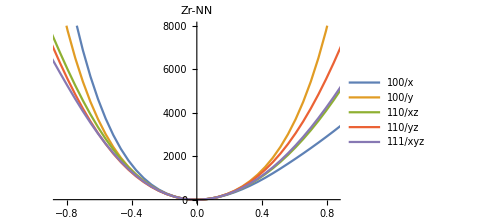

```mathematica
ListLinePlot[Table[zrdataAllDir[[i]][[5]],{i,1,5}],PlotRange->{{-0.85,0.85},{0,8000}},ImageSize->Medium,PlotLegends->Table[labelsZr[[i]],{i,1,Length@labelsZr}],PlotLabel->"Zr-NN"]
```

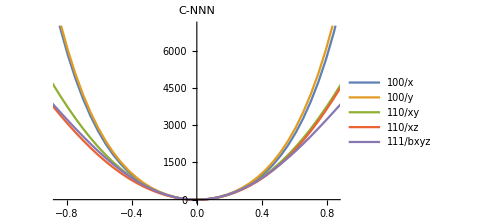

```mathematica
ListLinePlot[Table[cdataAllDir[[i]][[5]],{i,1,5}],PlotRange->{{-0.85,0.85},{0,7000}},ImageSize->Medium,PlotLegends->Table[labelsC[[i]],{i,1,Length@labelsC}],PlotLabel->"C-NNN"]
```

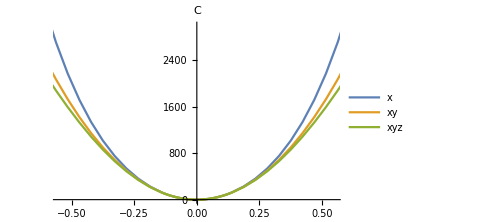

```mathematica
ListLinePlot[Table[cdataPerfAllDir[[i]][[5]],{i,1,3}],PlotRange->{{-0.55,0.55},{0,3000}},ImageSize->Medium,PlotLegends->Table[labelsCperf[[i]],{i,1,Length@labelsCperf}],PlotLabel->"C"]
```

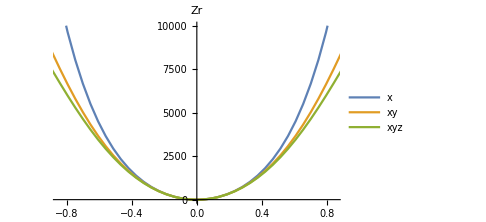

```mathematica
ListLinePlot[Table[zrdataPerfAllDir[[i]][[5]],{i,1,3}],PlotRange->{{-0.85,0.85},{0,10000}},ImageSize->Medium,PlotLegends->Table[labelsZrperf[[i]],{i,1,Length@labelsZrperf}],PlotLabel->"Zr"]
```

#### Taylor expand potential about equilibrium coords

```mathematica
(*Multivariate Taylor expansion*)
multiTaylor[f_,{vars_?VectorQ,pt_?VectorQ,n_Integer?NonNegative}]:=Sum[Nest[(vars-pt).#&,(D[f,{vars,k}]/.Thread[vars->pt]),k]/k!,{k,0,n},Method->"Procedural"]
```

```mathematica
Clear[trialFunction];Clear[trial]
```

```mathematica
(*6th order Taylor expansion, in list form*)

trial=(MonomialList@Expand@Flatten@Simplify@multiTaylor[V[x,y,z],{{x,y,z},{0,0,0},6}]);
trialFunction[{xx_,yy_,zz_}]:=trial/.{x->xx,y->yy,z->zz};
(*Number of terms in 3d to sixth order is 84!*)
trialFunction[{x,y,z}];
```

```mathematica
symmetrize3d[f_]:=With[{n=Length[h3d]},Function[{x,y,z},1/n*Total@Map[Composition[f,#][{x,y,z}]&,h3d]]]
symmetrize3d[trialFunction][x,y,z];
```

#### Symmetry

Define symmetry operations.
Make point groups for different environments.
Check terms in the trial function (Taylor expansion) invariant under point group operations

```mathematica
(*Point group symmetry elements*)
id3d={#[[1]],#[[2]],#[[3]]}&;
reflectx3d={-#[[1]],#[[2]],#[[3]]}&;
reflecty3d={#[[1]],-#[[2]],#[[3]]}&;
reflectz3d={#[[1]],-#[[2]],-#[[3]]}&;
inverse3d=-{#[[1]],#[[2]],#[[3]]}&;
(*Point group for id, x-reflect, y-reflect, z-reflect, inverse*)
h3dnnn={id3d,reflecty3d};
h3dnn={id3d,reflecty3d,reflectz3d};
h3d={id3d,reflectx3d,reflecty3d,reflectz3d,inverse3d};

symmetrize[f_,pointGroup_]:=With[{n=Length[pointGroup]},   Function[{x,y,z},1/n*Total@Map[Composition[f,#][{x,y,z}]&,pointGroup]]]

Vnnn[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3dnnn][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]

Vnn[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3dnn][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]
Vperf[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3d][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]
```

```mathematica
symmetrize[trialFunction,h3d][x,y,z];
trialFunction[{x,y,z}];
```

```mathematica
Vperf[x,y,z];
```

#### Fit the symmetry-reduced Taylor form, to the displacement vector energy data

Since the DFT data is in scalar vs energy form, convert it to vector vs energy form
In the fit we need to specify the coefficients, so extract the coefficients from the Taylor form

```mathematica
vectorise[arg_,vector_]:=Table[Table[Flatten[{arg[[vol]][[disp]][[1]]*vector,arg[[vol]][[disp]][[2]]}],{disp,1,Length@arg[[1]]}],{vol,1,Length@arg}];
VnnnCoeffs=List@@Total@Flatten@CoefficientList[Vnnn[x,y,z],{x,y,z}];
VnnCoeffs=List@@Total@Flatten@CoefficientList[Vnn[x,y,z],{x,y,z}];
VperfCoeffs=List@@Total@Flatten@CoefficientList[Vperf[x,y,z],{x,y,z}];
```

```mathematica
VnnnCoeffs;
```

```mathematica
dataCvector=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataXY,{1,1,0}][[1]],vectorise[CdataXY,{0,1,1}][[1]],vectorise[CdataXY,{1,0,1}][[1]],vectorise[CdataXZ,{1,0,-1}][[1]],vectorise[CdataXYZ,{1,1,1}][[1]],vectorise[CdataXYZ,{1,-1,1}][[1]],vectorise[CdataBXYZ,{-1,1,1}][[1]],vectorise[CdataBXYZ,{1,1,-1}][[1]]},4];

dataZrvector=Partition[Flatten@{vectorise[ZrdataX,{1,0,0}][[1]],vectorise[ZrdataY,{0,1,0}][[1]],vectorise[ZrdataY, {0,0,1}][[1]],vectorise[ZrdataXY,{1,1,0}][[1]],vectorise[ZrdataXY,{1,0,1}][[1]],vectorise[ZrdataYZ,{0,1,1}][[1]],vectorise[ZrdataXYZ,{1,1,1}][[1]]},4];

dataCvectorPerf=Partition[Flatten@{vectorise[CdataPerfX,{1,0,0}][[1]],vectorise[CdataPerfX,{0,1,0}][[1]],vectorise[CdataPerfX,{0,0,1}][[1]],vectorise[CdataPerfXY,{1,1,0}][[1]],vectorise[CdataPerfXY,{0,1,1}][[1]],vectorise[CdataPerfXY,{1,0,1}][[1]],vectorise[CdataPerfXYZ,{1,1,1}][[1]]},4];

dataZrvectorPerf=Partition[Flatten@{vectorise[ZrdataPerfX,{1,0,0}][[1]],vectorise[ZrdataPerfX,{0,1,0}][[1]],vectorise[ZrdataPerfX,{0,0,1}][[1]],vectorise[ZrdataPerfXY,{1,1,0}][[1]],vectorise[ZrdataPerfXY,{0,1,1}][[1]],vectorise[ZrdataPerfXY,{1,0,1}][[1]],vectorise[ZrdataPerfXYZ,{1,1,1}][[1]]},4];
```

```mathematica
(*
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{1/Sqrt[2],1/Sqrt[2],0}][[1]],vectorise[CdataXY,{0,1/Sqrt[2],1/Sqrt[2]}][[1]],vectorise[CdataXZ,{0,1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXZ,{0,-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3]}][[1]]},4];
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{Sqrt[2],Sqrt[2],0}][[1]],vectorise[CdataXY,{0,Sqrt[2],Sqrt[2]}][[1]],vectorise[CdataXY,{Sqrt[2],0,Sqrt[2]}][[1]],vectorise[CdataXZ,{Sqrt[2],0,-Sqrt[2]}][[1]],vectorise[CdataXYZ,{Sqrt[3],Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataXYZ,{Sqrt[3],-Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-Sqrt[3],Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataBXYZ,{Sqrt[3],Sqrt[3],-Sqrt[3]}][[1]]},4];
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{1/Sqrt[2],1/Sqrt[2],0}][[1]],vectorise[CdataXY,{0,1/Sqrt[2],1/Sqrt[2]}][[1]],vectorise[CdataXY,{1/Sqrt[2],0,1/Sqrt[2]}][[1]],vectorise[CdataXZ,{1/Sqrt[2],0,-1/Sqrt[2]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3]}][[1]]},4];*)
```

```mathematica
(dataCvector//Length)/11
get2dProjection[arg_,p1_,p2_]:=Transpose[{Transpose[arg][[p1]],Transpose[arg][[p2]],Transpose[arg][[-1]]}]
get1dProjection[arg_,p1_]:=Transpose[{Transpose[arg][[p1]],Transpose[arg][[-1]]}]
```

65

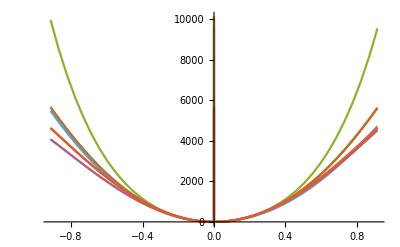

```mathematica
ListLinePlot@Partition[get1dProjection[dataCvector,3],Length[get1dProjection[dataCvector,1]]/11]
```

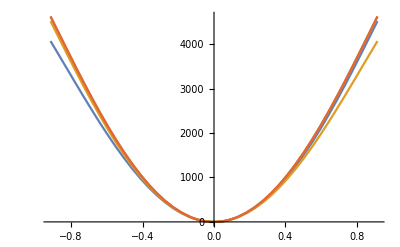

```mathematica
ListLinePlot@Partition[get1dProjection[dataCvector,2],Length[get1dProjection[dataCvector,1]]/11][[8;;11]]
```

```mathematica
ListPlot3D[get2dProjection[data,1,3],AxesLabel->{"x","y","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

-Graphics3D-

```mathematica
ListPlot3D[get2dProjection[data,1,3],AxesLabel->{"x","y","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

-Graphics3D-

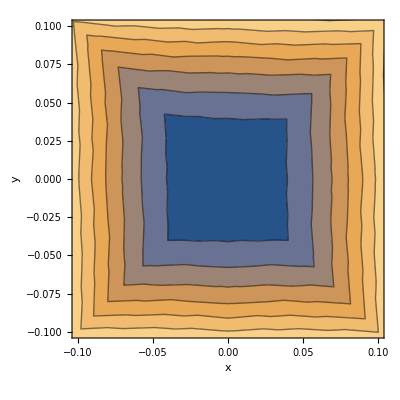

```mathematica
ListContourPlot[get2dProjection[data,1,3],AxesLabel->{"x","y","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

```mathematica
get2dProjection[data,2,3];
```

```mathematica
ListPlot3D[get2dProjection[data,2,3],AxesLabel->{"x","y","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

-Graphics3D-

```mathematica
ListPlot3D[get2dProjection[data,1,2],AxesLabel->{"x","y","z"},PlotRange->{{-0.25,0.25},{-0.25,0.25},{0,500}}]
```

-Graphics3D-

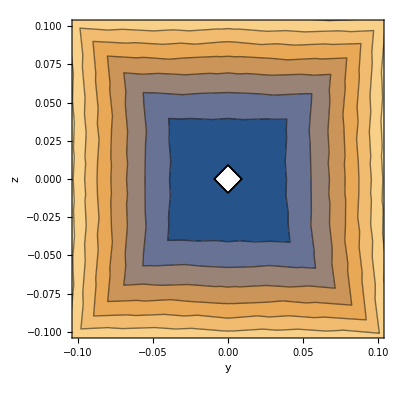

```mathematica
ListContourPlot[get2dProjection[data,2,3],FrameLabel->{"y","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

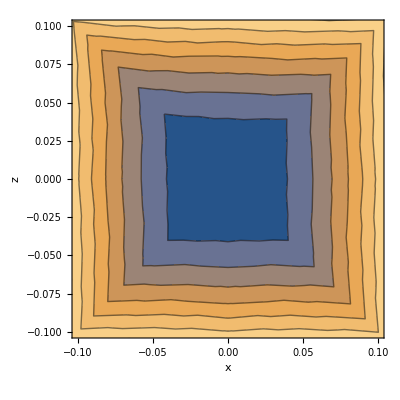

```mathematica
ListContourPlot[get2dProjection[data,1,3],FrameLabel->{"x","z"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

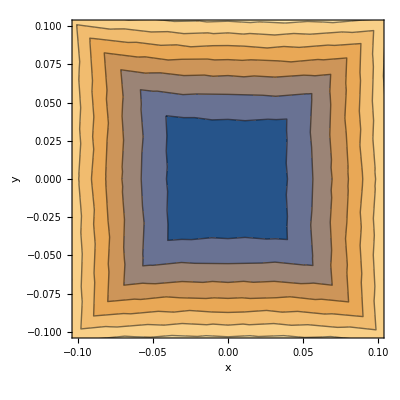

```mathematica
ListContourPlot[get2dProjection[data,1,2],FrameLabel->{"x","y"},PlotRange->{{-0.1,0.1},{-0.1,0.1},{0,80}}]
```

```mathematica
Partition[get2dProjection[data,1,3],Length[get2dProjection[data,1,3]]/11][[6;;7;;1]]
```

{{{-0.915,-0.915,5648.48},{-0.86925,-0.86925,5094.2},{-0.8235,-0.8235,4563.4},{-0.77775,-0.77775,4058.6},{-0.732,-0.732,3581.71},{-0.68625,-0.68625,3134.12},{-0.6405,-0.6405,2716.75},{-0.59475,-0.59475,2330.12},{-0.549,-0.549,1974.47},{-0.50325,-0.50325,1649.76},{-0.4575,-0.4575,1355.75},{-0.41175,-0.41175,1092.08},{-0.366,-0.366,858.26},{-0.32025,-0.32025,653.74},{-0.2745,-0.2745,477.98},{-0.22875,-0.22875,330.42},{-0.183,-0.183,210.54},{-0.13725,-0.13725,117.89},{-0.1281,-0.1281,102.59},{-0.11895,-0.11895,88.37},{-0.1098,-0.1098,75.21},{-0.10065,-0.10065,63.12},{-0.0915,-0.0915,52.09},{-0.08235,-0.08235,42.13},{-0.0732,-0.0732,33.22},{-0.06405,-0.06405,25.38},{-0.0549,-0.0549,18.59},{-0.04575,-0.04575,12.86},{-0.0366,-0.0366,8.18},{-0.02745,-0.02745,4.56},{-0.0183,-0.0183,1.98},{-0.00915,-0.00915,0.46},{0.,0.,0.},{0.00915,0.00915,0.58},{0.0183,0.0183,2.22},{0.02745,0.02745,4.9},{0.0366,0.0366,8.64},{0.04575,0.04575,13.43},{0.0549,0.0549,19.28},{0.06405,0.06405,26.17},{0.0732,0.0732,34.13},{0.08235,0.08235,43.13},{0.0915,0.0915,53.2},{0.10065,0.10065,64.32},{0.1098,0.1098,76.5},{0.11895,0.11895,89.75},{0.1281,0.1281,104.06},{0.13725,0.13725,119.43},{0.183,0.183,212.37},{0.22875,0.22875,332.34},{0.2745,0.2745,479.75},{0.32025,0.32025,655.07},{0.366,0.366,858.82},{0.41175,0.41175,1091.54},{0.4575,0.4575,1353.78},{0.50325,0.50325,1646.},{0.549,0.549,1968.61},{0.59475,0.59475,2321.85},{0.6405,0.6405,2705.78},{0.68625,0.68625,3120.22},{0.732,0.732,3564.69},{0.77775,0.77775,4038.35},{0.8235,0.8235,4539.92},{0.86925,0.86925,5067.63},{0.915,0.915,5619.12}},{{-0.915,0.915,4712.2},{-0.86925,0.86925,4278.85},{-0.8235,0.8235,3858.23},{-0.77775,0.77775,3453.13},{-0.732,0.732,3065.92},{-0.68625,0.68625,2698.45},{-0.6405,0.6405,2352.21},{-0.59475,0.59475,2028.34},{-0.549,0.549,1727.64},{-0.50325,0.50325,1450.69},{-0.4575,0.4575,1197.83},{-0.41175,0.41175,969.25},{-0.366,0.366,765.01},{-0.32025,0.32025,585.07},{-0.2745,0.2745,429.37},{-0.22875,0.22875,297.8},{-0.183,0.183,190.27},{-0.13725,0.13725,106.72},{-0.1281,0.1281,92.89},{-0.11895,0.11895,80.01},{-0.1098,0.1098,68.09},{-0.10065,0.10065,57.13},{-0.0915,0.0915,47.12},{-0.08235,0.08235,38.08},{-0.0732,0.0732,30.},{-0.06405,0.06405,22.87},{-0.0549,0.0549,16.71},{-0.04575,0.04575,11.51},{-0.0366,0.0366,7.28},{-0.02745,0.02745,4.01},{-0.0183,0.0183,1.7},{-0.00915,0.00915,0.36},{0.,0.,0.},{0.00915,-0.00915,0.6},{0.0183,-0.0183,2.17},{0.02745,-0.02745,4.72},{0.0366,-0.0366,8.25},{0.04575,-0.04575,12.75},{0.0549,-0.0549,18.24},{0.06405,-0.06405,24.71},{0.0732,-0.0732,32.16},{0.08235,-0.08235,40.61},{0.0915,-0.0915,50.04},{0.10065,-0.10065,60.47},{0.1098,-0.1098,71.9},{0.11895,-0.11895,84.33},{0.1281,-0.1281,97.77},{0.13725,-0.13725,112.21},{0.183,-0.183,199.68},{0.22875,-0.22875,312.96},{0.2745,-0.2745,452.6},{0.32025,-0.32025,619.26},{0.366,-0.366,813.61},{0.41175,-0.41175,1036.36},{0.4575,-0.4575,1288.21},{0.50325,-0.50325,1569.82},{0.549,-0.549,1881.77},{0.59475,-0.59475,2224.52},{0.6405,-0.6405,2598.34},{0.68625,-0.68625,3003.31},{0.732,-0.732,3439.2},{0.77775,-0.77775,3905.45},{0.8235,-0.8235,4401.07},{0.86925,-0.86925,4924.61},{0.915,-0.915,5474.03}}}

```mathematica
ListPointPlot3D@Partition[get2dProjection[data,1,2],Length[get2dProjection[data,1,2]]/11][[1;;2;;1]]
```

-Graphics3D-

```mathematica
ListPointPlot3D@Partition[get2dProjection[data,1,3],Length[get2dProjection[data,1,3]]/11][[6;;7;;1]]
```

-Graphics3D-

```mathematica
ListPointPlot3D@Partition[get2dProjection[data,1,2],Length[get2dProjection[data,1,2]]/11][[4;;5;;1]]
```

-Graphics3D-

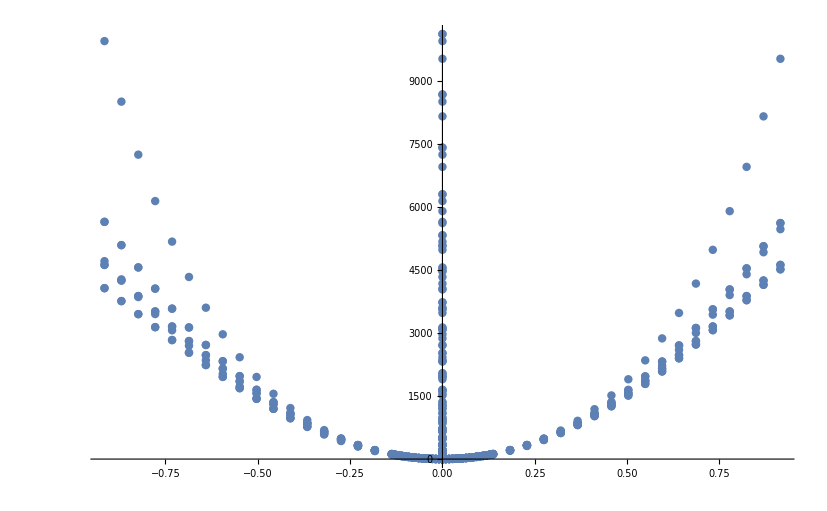

```mathematica
ListPlot@get1dProjection[data,1]
```

```mathematica
ListPlot3D@get2dProjection[data,1,2]
```

-Graphics3D-

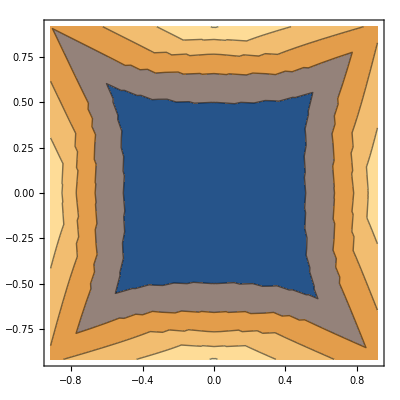

```mathematica
ListContourPlot@get2dProjection[data,1,2]
```

```mathematica
varGetter[arg_]:=If[Length@arg==2,arg[[2]],If[Length@arg==3,arg,0]]
coeffListVar=varGetter/@coeffList;
```

```mathematica
data//Dimensions;
```

```mathematica
nlm=NonlinearModelFit[data,Vnnn[x,y,z],coeffListVar,{x,y,z}]
```

FittedModel[46.7687+5.8993 x+«73»]

```mathematica
nlmF[xx_,yy_,zz_]:=nlm["BestFit"]/.{x->xx,y->yy,z->zz}
nlmF[x,y,0]
```

46.7687+5.8993 x+2375.93 x^2-136.647 x^3+12398.3 x^4-189.982 x^5-1061.23 x^6+2344.51 y^2+8.86727 x y^2-14193.1 x^2 y^2+164.006 x^3 y^2-4748.7 x^4 y^2+14193. y^4+164.006 x y^4-4748.7 x^2 y^4-2562.86 y^6

```mathematica
Plot3D[nlmF[0,y,z],{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[nlmF[x,0,z],{x,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[nlmF[x,y,0],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Options[ContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
With[{a=0.07},ContourPlot3D[nlmF[x,y,z],{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
With[{a=0.15},ContourPlot3D[nlmF[x,y,z],{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
With[{a=0.25},ContourPlot3D[nlmF[x,y,z],{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
With[{a=0.5},ContourPlot3D[nlmF[x,y,z],{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
With[{a=0.75},ContourPlot3D[nlmF[x,y,z],{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
ContourPlot3D[nlmF[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,y,z,Cos[x]+Cos[y]*Cos[z]+RandomReal[{-0.1,0.25}]},{x,5},{y,5},{z,5}],1];
```

```mathematica
varGetter[arg_]:=If[Length@arg==2,arg[[2]],If[Length@arg==3,arg,0]]
coeffListVar=varGetter/@coeffList;
Partition[Flatten@data,4];
```

```mathematica
flatData=Partition[Flatten@data,4];
```

```mathematica
nlm=NonlinearModelFit[flatData,Vnnn[x,y,z],coeffListVar,{x,y,z}]
```

FittedModel[4.74114-2.59319 x+0.237936 x^2+«65»+0.000438521 y^2 z^4-0.00362019 z^5-0.00142884 x z^5+0.000608286 z^6]

```mathematica
nlm["BestFit"]
```

4.74114-2.59319 x+0.237936 x^2+0.0603326 x^3-0.000311762 x^4-0.00119881 x^5+0.0000545941 x^6-0.604786 y^2+0.113203 x y^2-0.0443132 x^2 y^2+0.00879598 x^3 y^2-0.000627529 x^4 y^2+0.0167489 y^4-3.55497×10^-6 x y^4-0.000093043 x^2 y^4+0.000153633 y^6-3.39111 z+2.29242 x z-0.732068 x^2 z+0.00512446 x^3 z+0.025358 x^4 z-0.00282045 x^5 z+0.549348 y^2 z-0.0578326 x y^2 z+0.0100463 x^2 y^2 z-0.000561661 x^3 y^2 z-0.0199143 y^4 z+0.00016646 x y^4 z+0.66131 z^2-0.675822 x z^2+0.345635 x^2 z^2-0.0531002 x^3 z^2+0.00310517 x^4 z^2-0.0766006 y^2 z^2+0.00969704 x y^2 z^2-0.000848711 x^2 y^2 z^2+0.00312007 y^4 z^2+0.0769033 z^3-0.0233304 x z^3-0.0238493 x^2 z^3+0.00189102 x^3 z^3-0.00378685 y^2 z^3-0.000576966 x y^2 z^3-0.0151027 z^4+0.0185392 x z^4+0.000386932 x^2 z^4+0.000438521 y^2 z^4-0.00362019 z^5-0.00142884 x z^5+0.000608286 z^6

```mathematica
nlmF[xx_,yy_,zz_]:=nlm["BestFit"]/.{x->xx,y->yy,z->zz}
nlmF[x,y,0]
```

```mathematica
nlmF[x,y,0]
```

4.74114-2.59319 x+0.237936 x^2+0.0603326 x^3-0.000311762 x^4-0.00119881 x^5+0.0000545941 x^6-0.604786 y^2+0.113203 x y^2-0.0443132 x^2 y^2+0.00879598 x^3 y^2-0.000627529 x^4 y^2+0.0167489 y^4-3.55497×10^-6 x y^4-0.000093043 x^2 y^4+0.000153633 y^6

```mathematica
ListPlot3D@Transpose[{Transpose[flatData][[1]],Transpose[flatData][[2]],Transpose[flatData][[4]]}]
```

-Graphics3D-

```mathematica
Plot3D[nlmF[x,y,0],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

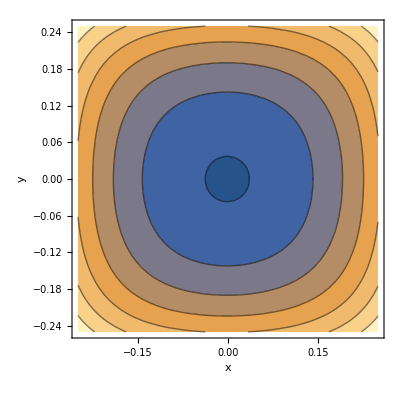

```mathematica
With[{p=0.25},ContourPlot[nlmF[x,y,0],{x,-p,p},{y,-p,p},FrameLabel->{"x","y"}]]
```

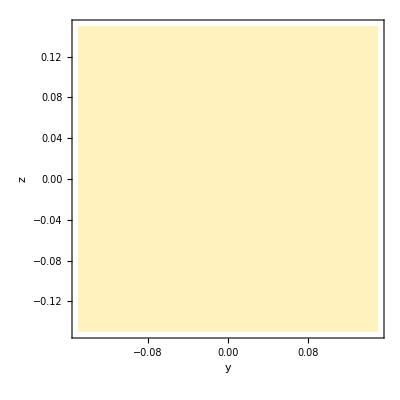

```mathematica
With[{p=0.15},ContourPlot[nlmF[x,y,0],{x,-p,p},{y,-p,p},Contours->Function[{min,max},Range[min,max,0.1]],FrameLabel->{"y","z"},ContourLabels->True]]
```

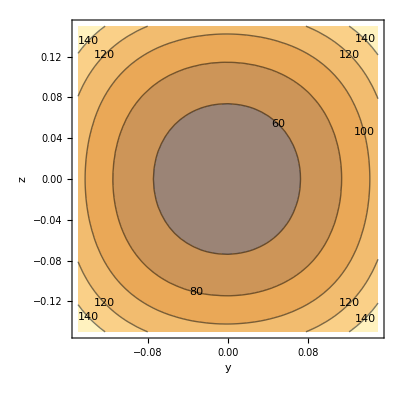

```mathematica
With[{p=0.15},ContourPlot[nlmF[x,y,0],{x,-p,p},{y,-p,p},FrameLabel->{"y","z"},ContourLabels->True,Contours->{40,60,80,100,120,140}]]
```

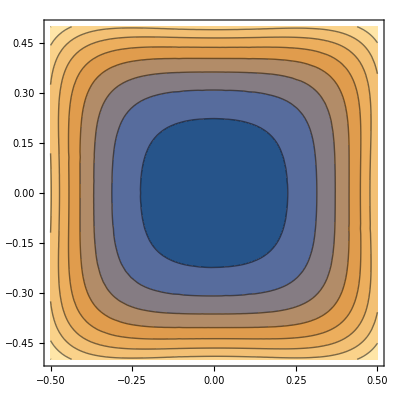

```mathematica
ContourPlot[nlmF[x,y,0],{x,-0.5,0.5},{y,-0.5,0.5}]
```

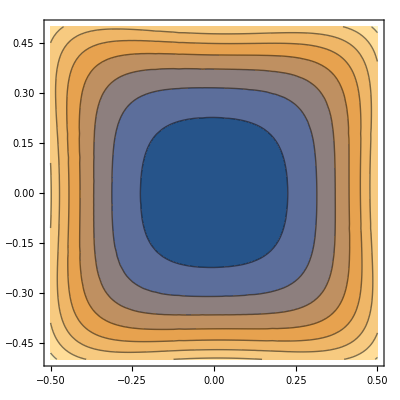

```mathematica
ContourPlot[nlmF[x,0,z],{x,-0.5,0.5},{z,-0.5,0.5}]
```

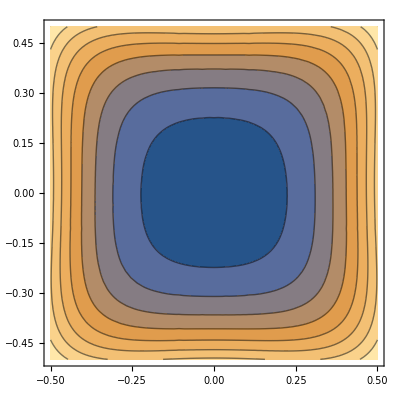

```mathematica
ContourPlot[nlmF[0,y,z],{y,-0.5,0.5},{z,-0.5,0.5}]
```